## Solar Flares & CMEs Problem Set 2 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 1

### Part a.

#### Declare the assumptions for this problem

```mathematica
$Assumptions =  λ >0&& z>0 && b > 0  && c >0 && Ics> 0 && h >0;
```

#### The flux function for this problem is given by

```mathematica
A[y_,z_] = λ ArcTan[(y+b)/z]-λ ArcTan[(y-b)/z] + Ics/c Log[(y^2 + (z+h)^2)/(y^2+(z-h)^2)];
```

#### Plot this function to ensure that it has the correct behaviour

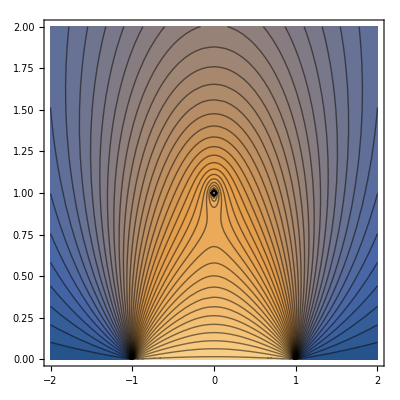

```mathematica
ContourPlot[A[y,z] /. {b-> 1,λ-> 1, h-> 1, Ics-> 0.1, c-> 1},{y,-2,2},{z,0,2},Contours->50]
```

#### The reconnection flux is measured between the origin and the X-point. Find the X-point by setting the magnetic field on the y-axis equal to zero and solve for the height z. Find the magnetic field by taking a curl.

```mathematica
B = Cross[Grad[A[y,z],{x,y,z}],{1,0,0}] /. y->0//FullSimplify
```

{0,(4 h Ics)/(c h^2-c z^2)-(2 b λ)/(b^2+z^2),0}

#### Solve for the height of the X-point

```mathematica
zx = Part[Solve[B[[2]]==0,z] //FullSimplify,2,1,2]
```

√((b h (-2 b Ics+c h λ))/(2 h Ics+b c λ))

#### Expand this solution for a high-lying rope (h >> b)

```mathematica
zxa =Normal[Series[zx  //FullSimplify,{h,Infinity,0}]] /. λ-> 2 Ics /c //FullSimplify
```

√(b h)

#### Plug this expression into the flux function and continue the approximation

```mathematica
(ψr=Series[A[0,zxa],{h,Infinity,1}] /.  λ-> 2 Ics /c//Normal //FullSimplify) //Framed
```

(8 √(b/h) Ics)/c

### Part b.

#### The measured CME velocity is given as

```mathematica
v = v0/2(Tanh[(t - 2 τ)/τ]+1);
```

```mathematica
h =Integrate[v,t]
```

(t v0)/2+1/2 v0 τ Log[Cosh[(t-2 τ)/τ]]

```mathematica
ψr
```

(8 Ics √(b/((t v0)/2+1/2 v0 τ Log[Cosh[(t-2 τ)/τ]])))/c